```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
PureIntegrals=ReadList[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasis5.txt"}]];
PureIntegrals2=PureIntegrals/.{mTsq->mt2};
```

```mathematica
OldProps={(k[2]-p[2])^2,(k[1]+p[1]+p[2]+p[3]+p[4]+p[5])^2};
NewProps[1]=Expand[Expand[OldProps[[1]]]/.loopMomentumScalarProducts/.mandelstamScalarProducts/.kinematics]
NewProps[2]=Expand[Expand[OldProps[[2]]]/.loopMomentumScalarProducts/.mandelstamScalarProducts/.kinematics]
PureIntegrals3=Expand[PureIntegrals2/.DB[n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_,n9_]:>hxb[n1,n2,n3,n4,n5,0,0,n6,n7,0,0,0,0](NewProps[1])^-n8(NewProps[2])^-n9];
Export[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasisDB1.txt"}],PureIntegrals3]
PureIntegrals[[31]]
PureIntegrals3[[31]]
```

s12-PR[5]+PR[9]+PR[13]

-s12-3 PR[1]+PR[3]+PR[10]+PR[11]+PR[12]

/home/dschiebe/Documents/lanayru/PhD_Files/PureInts_ttH/HexaBox1/files/PureIntegralBasisDB1.txt

-ep^3 mTsq s12 DB[0,1,0,2,1,1,1,0,0]+ep^3 s12 s345 DB[0,1,0,2,1,1,1,0,0]+1/2 ep^3 mTsq s12 DB[0,1,1,2,0,1,1,0,0]-1/2 ep^3 s12 s345 DB[0,1,1,2,0,1,1,0,0]+ep^4 s12^2 DB[1,1,1,1,1,1,1,0,-1]-ep^4 mTsq s12^2 DB[1,1,1,1,1,1,1,0,0]

-ep^3 mt2 s12 hxb[0,1,0,2,1,0,0,1,1,0,0,0,0]+ep^3 s12 s345 hxb[0,1,0,2,1,0,0,1,1,0,0,0,0]-3 ep^4 s12^2 hxb[0,1,1,1,1,0,0,1,1,0,0,0,0]+1/2 ep^3 mt2 s12 hxb[0,1,1,2,0,0,0,1,1,0,0,0,0]-1/2 ep^3 s12 s345 hxb[0,1,1,2,0,0,0,1,1,0,0,0,0]+ep^4 s12^2 hxb[1,1,0,1,1,0,0,1,1,0,0,0,0]+ep^4 s12^2 hxb[1,1,1,1,1,0,0,1,1,-1,0,0,0]+ep^4 s12^2 hxb[1,1,1,1,1,0,0,1,1,0,-1,0,0]+ep^4 s12^2 hxb[1,1,1,1,1,0,0,1,1,0,0,-1,0]-ep^4 mt2 s12^2 hxb[1,1,1,1,1,0,0,1,1,0,0,0,0]-ep^4 s12^3 hxb[1,1,1,1,1,0,0,1,1,0,0,0,0]

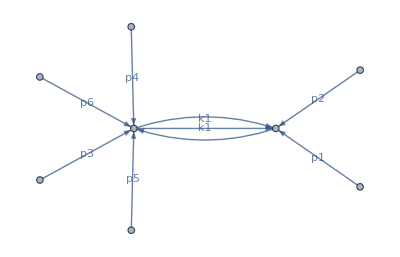

```mathematica
plotDiagram[hxb[1,0,0,1,1,0,0,0,0,0,0,0,0]]
```